## LECs declaration

LCDa = Johannes parameters
LCDb = E2: -1      MeV    E3: -3       MeV  from PJM paper
LCDc = E2: -2.22 MeV    E3: -8.48  MeV Nuclear case
LCDd = Unitary               E3: -10 MeV

```mathematica
(* Johannes fitting parameters a=12 c.a. *)
LCDo={{25, 0.40386299,-2929.4763,89436.1852}};
```

```mathematica
(* Johannes fitting parameters a=12 c.a. *)
LCDa={{0.0025, 0.01085409,-1.106057,-1.159333},
{0.0900, 0.01085514,-13.493590, 2.150388},
{0.3025, 0.01085640,-39.797327, 24.965545},
{0.6400, 0.01085554,-80.013554, 81.336340},
{1.1025, 0.01085210,-134.141484, 191.491264},
{1.6900, 0.01085481,-202.185387, 379.175010},
{2.4025, 0.01085130,-284.138103, 683.999621},
{3.2400, 0.01086136,-380.015170, 1143.332900},
{4.2025, 0.01085691,-489.792808, 1884.506079},
{5.2900, 0.01085517,-613.485357, 2977.884003},
{6.5025, 0.01084950,-751.085499, 4589.004608},
{7.8400, 0.01084884,-902.604164, 7067.645881},
{9.3025, 0.01084997,-1068.038344, 10667.304476},
{10.8900, 0.01085217,-1247.387431, 16133.941591},
{12.6025, 0.01085409,-1440.650123, 24382.008195},
{14.4400, 0.01084667,-1647.808037, 36688.658380},
{16.4025, 0.01085322,-1868.905655, 52963.123627},
{18.4900, 0.01087420,-2103.948323, 80952.129573},
{20.7025, 0.01085536,-2352.819143, 119013.695269},
{23.0400, 0.01085344,-2615.638250, 190732.889176}};
```

```mathematica
(* E2=1 E3=3 *)
LCDb={{0.05,1,-1.55166500,0.1329927285},{0.1,1,-2.24166300,0.3701120098},{0.16,1,-3.44040000,1.138524898},{0.2,1,-4.04022700,1.249910638},{0.3,1,-6.39651000,2.799024416},{0.35,1,-7.80830000,3.936630847},{0.4,1,-9.31007578,5.177438097},{0.45,1,-10.97613646,6.72964684},{0.5,1,-12.78163000,8.552092744},{0.55,1,-14.72581116,10.66423485},{0.6,1,-16.80907468,13.08996044},{0.65,1,-19.03174482,15.85408},{0.7,1,-21.39405000,18.9824788},{0.75,1,-23.89403709,22.49131818},{0.8,1,-26.53580000,26.42858035},{0.9,1,-32.23375000,35.64420878},{0.95,1,-35.29122000,40.98921369},{1,1,-38.48853000,46.87432648},{1.05,1,-41.82441000,53.32423158},{1.1,1,-45.29949000,60.37950916},{1.2,1,-52.66596000,76.44622944},{1.5,1,-78.11106000,143.6179272},{2,1,-131.64598000,346.2149284},{3,1,-280.45691000,1468.17912},{4,1,-484.92093000,5254.800421},{6,1,-1060.79670000,61617.93639},{10,1,-2880.38650000,12838191.7}};
```

```mathematica
(* Nuclear E2=2.22 E3=8.48 *)
LCDc={{0.1,1,	0	,0},{0.16,1,-5.23609711,-0.2508527567},{0.2,1,-6.21155090,-0.01411577035},{0.3,1,-9.04089890,0.9058334635},{0.35,1,-10.66481819,1.562725218},{0.4,1,-12.42824554,2.36543082},{0.45,1,-14.33104515,3.3244409},{0.5,1,-16.37322998,4.450396189},{0.55,1,-18.55475197,5.753778748},{0.6,1,-20.87557983,7.245120228},{0.65,1,-23.33569527,8.935015304},{0.7,1,-25.93508911,10.83416803},{0.75,1,-28.67371368,12.95315533},{0.8,1,-31.55156555,15.30282946},{0.85,1,-34.56868362,17.89442822},{0.9,1,-37.72501221,20.7388847},{0.95,1,-41.02048416,23.84721094},{1,1,-44.45520020,27.23128363},{1.05,1,-48.02915573,30.90286676},{1.1,1,-51.74223328,34.87341855},{1.2,1,-59.58599854,43.76101396},{1.5,1,-86.45745087,78.9169705},{2,1,-142.37614441,172.7038298},{3,1,-295.95935059,559.0134636},{4,1,-505.20166016,1397.569451},{6,1,-1090.66113281,6311.303676},{10,1,-2929.47631836,89436.18522}};
```

```mathematica
(*Unitary E3=10*)
LCDd={{3,1,-250.617,101.932316},{4,1,-445.542,327.529341},{5,1,-696.159,726.927273},{6,1,-1002.47,1363.978137},{7,1,-1364.47,2321.631926},{8,1,-1782.17,3709.828715}};
```

## Solvers

```mathematica
RiccatiBesselJ[z_,l_]:=z SphericalBesselJ[l,z];
RiccatiBesselN[z_,l_]:=z SphericalBesselY[l,z];
```

```mathematica
alpha[r_,k_,l_,h_]:=(1+h (D[FunctionExpand[RiccatiBesselN[k x,l]],x]/.x->r)/(FunctionExpand[RiccatiBesselN[k r,l]]))
beta[r_,k_,l_,h_]:=h FunctionExpand[RiccatiBesselJ[k r,l]](((D[FunctionExpand[RiccatiBesselJ[k x,l]],x])/.x->r)/(FunctionExpand[RiccatiBesselJ[k r,l]])-((D[FunctionExpand[RiccatiBesselN[k x,l]],x])/.x->r)/(FunctionExpand[RiccatiBesselN[k r,l]]))
```

```mathematica
SolveSecularNL0[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ]:=Block[{p,RRmax,nnGrid,hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,asywf,wf,wffree,Tere,fit,nn,δ,L,r,mod,usol},
p=momentum;
RRmax=Rdis;
nnGrid=Npoints;
hDif=RRmax/nnGrid;

(* Matrix components *)
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{nnGrid,nnGrid}];
Dmat=DiagonalMatrix[Table[hDif^2 (p^2-mh2 V0[i hDif]),{i,1,nnGrid}]];
Wmat=Table[-hDif^3 mh2 WS[i hDif,j hDif,p],{i,1,nnGrid},{j,1,nnGrid}]; 

If[p==0,

bcol=Table[Which[i==nnGrid,-hDif,1==1,0],{i,1,nnGrid}];
Dmat⟦nnGrid⟧⟦nnGrid⟧+=1; (*this is only for 0 energy*)

ucol=Array[Subscript["u", ##]&,{nnGrid}];
Amat=Dmat+Wmat+Kmat;

usol=LinearSolve[Amat,bcol];
wf=Table[{i hDif,usol⟦i⟧},{i,1,nnGrid}];
Tere=RRmax-usol⟦-1⟧;
,

bcol=ConstantArray[0,nnGrid];
ucol=Array[Subscript["u", ##]&,{nnGrid}];
Amat=Dmat+Wmat+Kmat;
bcol⟦-1⟧=- hDif p(Cos[p RRmax]+Sin[p RRmax]Tan[p RRmax]);
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+1-hDif p Tan[p Rmax];

usol=LinearSolve[Amat,bcol];

wf=Table[{i hDif,usol⟦i⟧},{i,1,nnGrid}];
Tere=p^(2L+1) ((usol⟦-1⟧-Sin[p RRmax])/Cos[p RRmax])^-1;
];

{Tere,wf}
]
```

```mathematica
SolveSecularNL1[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ]:=Block[{p,RRmax,nnGrid,hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,asywf,wf,wffree,tanDelta,fit,nn,δ,L,r,mod,usol,lam,lec},
p=momentum;
RRmax=Rdis;
nnGrid=Npoints;
hDif=RRmax/nnGrid;
L=Lin;

(* Matrix components *)
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{nnGrid,nnGrid}];
Dmat=DiagonalMatrix[Table[hDif^2 (p^2-mh2 V0[i hDif]-(L(L+1))/(i hDif)^2),{i,1,nnGrid}]];
Wmat=Table[-hDif^3 mh2 WP[i hDif,j hDif,p],{i,1,nnGrid},{j,1,nnGrid}]; 

bcol=ConstantArray[0,nnGrid];
ucol=Array[Subscript["u", ##]&,{nnGrid}];
Amat=Dmat+Wmat+Kmat;

If[p==0,
(* ------------------------- zer0 momentum ------------------------- *)

If[L==0,
bcol⟦-1⟧=- hDif;
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+1
,
(* L≥1 *)
bcol[[-1]]=1-1./nnGrid;
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+hDif^2 nnGrid;
];

usol=LinearSolve[Amat,bcol];
wf=Table[{i hDif,usol⟦i⟧},{i,1,nnGrid}];

If[L==0,
tanDelta=RRmax-usol⟦-1⟧;
,
(* L≥1 *)
tanDelta=RRmax^3/3-usol⟦-1⟧ RRmax;
tanDelta=RRmax-usol⟦-1⟧;
];
,
(* ------------------------- non-zer0 momentum --------------------- *)

(*bcol⟦-1⟧=- hDif p(Cos[p RRmax]+Sin[p RRmax]Tan[p RRmax]);*)
bcol⟦-1⟧=- beta[RRmax,p,L,hDif];
(*Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+1-hDif p Tan[p RRmax];*)
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[RRmax,p,L,hDif];

usol=LinearSolve[Amat,bcol];

wf=Table[{i hDif,usol⟦i⟧},{i,1,nnGrid}];
tanDelta= (RiccatiBesselJ[p RRmax,L]/RiccatiBesselN[p RRmax,L])-(usol⟦-1⟧/RiccatiBesselN[p RRmax,L]);
];

{tanDelta,wf}
]
```

```mathematica
RRmax=1;L=0;
N[Limit[RiccatiBesselN[p RRmax,L],p->0]]
N[Limit[RiccatiBesselJ[p RRmax,L],p->0]]
```

-1.

0.

```mathematica
Scatt1[α0_?NumberQ]:=Block[{f,w},
c0=α0;
(* 1/2 is to have μ instead of m*)
f=Replace[w,NDSolve[{w'[r]+w[r]^2- mh2 Vα0[α0,r]==0,w[0]==10^20},w,{r,0,R}]⟦1,1⟧];R-f[R]^-1]
```

## Solve

```mathematica
(***********************)
(*  Physical quantities   *)
   (***********************)
(*m=1;μ=m/2;hbar=1;mh2=(2 μ)/(hbar)^2;e1=0.1;α=0;
Λl={2.,4.,6.,8.,10.};*)
```

```mathematica
(*
LCDa=Johannes parameters
LCDb=E2:-1 MeV E3:-3 MeV from PJM paper
LCDc=E2:-2.22 MeV E3:-8.48 MeV Nuclear case
LCDd=Unitary E3:-10 MeV
*)

LCD = LCDc;
m=938.92;
μ=m/2;
```

```mathematica
(* Options: *)
Fit2b = False;  (* Do you want to fit the two body lec?*)
aleph = 1/12;  (* In case to which aleph*)

CalculateFF=False;          (*Calcualte Fermion-Fermion scattering*)
CalculateDD =False;         (*Calcualte Dimer-Dimer scattering*)
CalculateDDstar=False; (*Calculate ab-ac scattering*)
Calculate4H =True;         (*Calculate a-abc scattering*)
```

{λ = ,0.1,   C0 = ,0,   D0 = ,0}

{ * Fermion - Trimer star scattering * }

α3 is 0.00792452

L = 0: (finite momentum)   a_(t - f) = 0.00191688     r_(t - f) = 119593.

L = 1: (finite momentum)   a_(t - f) = -0.0752082     r_(t - f) = -389.926

--

{λ = ,0.16,   C0 = ,-5.2361,   D0 = ,-0.250853}

{ * Fermion - Trimer star scattering * }

α3 is 0.00792452

L = 0: (finite momentum)   a_(t - f) = -0.0939306     r_(t - f) = -2508.36

L = 1: (finite momentum)   a_(t - f) = -0.0737916     r_(t - f) = -392.796

--

{λ = ,0.2,   C0 = ,-6.21155,   D0 = ,-0.0141158}

{ * Fermion - Trimer star scattering * }

α3 is 0.00792452

L = 0: (finite momentum)   a_(t - f) = -0.435655     r_(t - f) = -597.671

L = 1: (finite momentum)   a_(t - f) = -0.0737592     r_(t - f) = -393.036

--

{λ = ,0.3,   C0 = ,-9.0409,   D0 = ,0.905833}

{ * Fermion - Trimer star scattering * }

α3 is 0.00792452

L = 0: (finite momentum)   a_(t - f) = 0.0852084     r_(t - f) = 2612.98

L = 1: (finite momentum)   a_(t - f) = -0.0737711     r_(t - f) = -393.174

--

{λ = ,0.35,   C0 = ,-10.6648,   D0 = ,1.56273}

{ * Fermion - Trimer star scattering * }

α3 is 0.00792452

L = 0: (finite momentum)   a_(t - f) = 0.0617746     r_(t - f) = 3631.75

L = 1: (finite momentum)   a_(t - f) = -0.0737795     r_(t - f) = -393.191

--

{λ = ,0.4,   C0 = ,-12.4282,   D0 = ,2.36543}

{ * Fermion - Trimer star scattering * }

α3 is 0.00792452

L = 0: (finite momentum)   a_(t - f) = 0.0513252     r_(t - f) = 4385.95

L = 1: (finite momentum)   a_(t - f) = -0.0737842     r_(t - f) = -393.205

--

{λ = ,0.45,   C0 = ,-14.331,   D0 = ,3.32444}

{ * Fermion - Trimer star scattering * }

α3 is 0.00792452

L = 0: (finite momentum)   a_(t - f) = 0.0456521     r_(t - f) = 4940.05

L = 1: (finite momentum)   a_(t - f) = -0.073785     r_(t - f) = -393.221

--

{λ = ,0.5,   C0 = ,-16.3732,   D0 = ,4.4504}

{ * Fermion - Trimer star scattering * }

α3 is 0.00792452

L = 0: (finite momentum)   a_(t - f) = 0.0422685     r_(t - f) = 5341.33

L = 1: (finite momentum)   a_(t - f) = -0.0737825     r_(t - f) = -393.241

--

{λ = ,0.55,   C0 = ,-18.5548,   D0 = ,5.75378}

{ * Fermion - Trimer star scattering * }

α3 is 0.00792452

L = 0: (finite momentum)   a_(t - f) = 0.0401642     r_(t - f) = 5625.01

L = 1: (finite momentum)   a_(t - f) = -0.0737775     r_(t - f) = -393.263

--

{λ = ,0.6,   C0 = ,-20.8756,   D0 = ,7.24512}

{ * Fermion - Trimer star scattering * }

α3 is 0.00792452

L = 0: (finite momentum)   a_(t - f) = 0.0388523     r_(t - f) = 5817.44

L = 1: (finite momentum)   a_(t - f) = -0.0737703     r_(t - f) = -393.289

--

{λ = ,0.65,   C0 = ,-23.3357,   D0 = ,8.93502}

{ * Fermion - Trimer star scattering * }

α3 is 0.00792452

L = 0: (finite momentum)   a_(t - f) = 0.0380695     r_(t - f) = 5938.56

L = 1: (finite momentum)   a_(t - f) = -0.0737614     r_(t - f) = -393.318

--

{λ = ,0.7,   C0 = ,-25.9351,   D0 = ,10.8342}

{ * Fermion - Trimer star scattering * }

α3 is 0.00792452

L = 0: (finite momentum)   a_(t - f) = 0.037662     r_(t - f) = 6003.63

L = 1: (finite momentum)   a_(t - f) = -0.0737512     r_(t - f) = -393.348

--

{λ = ,0.75,   C0 = ,-28.6737,   D0 = ,12.9532}

{ * Fermion - Trimer star scattering * }

α3 is 0.00792452

L = 0: (finite momentum)   a_(t - f) = 0.0375334     r_(t - f) = 6024.45

L = 1: (finite momentum)   a_(t - f) = -0.0737399     r_(t - f) = -393.381

--

{λ = ,0.8,   C0 = ,-31.5516,   D0 = ,15.3028}

{ * Fermion - Trimer star scattering * }

α3 is 0.00792452

L = 0: (finite momentum)   a_(t - f) = 0.0376216     r_(t - f) = 6010.18

L = 1: (finite momentum)   a_(t - f) = -0.0737278     r_(t - f) = -393.414

--

{λ = ,0.85,   C0 = ,-34.5687,   D0 = ,17.8944}

{ * Fermion - Trimer star scattering * }

α3 is 0.00792452

L = 0: (finite momentum)   a_(t - f) = 0.0378845     r_(t - f) = 5967.98

L = 1: (finite momentum)   a_(t - f) = -0.073715     r_(t - f) = -393.449

--

{λ = ,0.9,   C0 = ,-37.725,   D0 = ,20.7389}

{ * Fermion - Trimer star scattering * }

α3 is 0.00792452

L = 0: (finite momentum)   a_(t - f) = 0.0382929     r_(t - f) = 5903.57

L = 1: (finite momentum)   a_(t - f) = -0.0737016     r_(t - f) = -393.485

--

{λ = ,0.95,   C0 = ,-41.0205,   D0 = ,23.8472}

{ * Fermion - Trimer star scattering * }

α3 is 0.00792452

L = 0: (finite momentum)   a_(t - f) = 0.0388259     r_(t - f) = 5821.53

L = 1: (finite momentum)   a_(t - f) = -0.0736879     r_(t - f) = -393.521

--

{λ = ,1,   C0 = ,-44.4552,   D0 = ,27.2313}

{ * Fermion - Trimer star scattering * }

α3 is 0.00792452

L = 0: (finite momentum)   a_(t - f) = 0.0394695     r_(t - f) = 5725.43

L = 1: (finite momentum)   a_(t - f) = -0.0736738     r_(t - f) = -393.558

--

{λ = ,1.05,   C0 = ,-48.0292,   D0 = ,30.9029}

{ * Fermion - Trimer star scattering * }

α3 is 0.00792452

L = 0: (finite momentum)   a_(t - f) = 0.0402134     r_(t - f) = 5618.19

L = 1: (finite momentum)   a_(t - f) = -0.0736594     r_(t - f) = -393.595

--

{λ = ,1.1,   C0 = ,-51.7422,   D0 = ,34.8734}

{ * Fermion - Trimer star scattering * }

α3 is 0.00792452

L = 0: (finite momentum)   a_(t - f) = 0.0410498     r_(t - f) = 5502.24

L = 1: (finite momentum)   a_(t - f) = -0.0736449     r_(t - f) = -393.633

--

{λ = ,1.2,   C0 = ,-59.586,   D0 = ,43.761}

{ * Fermion - Trimer star scattering * }

α3 is 0.00792452

L = 0: (finite momentum)   a_(t - f) = 0.0429837     r_(t - f) = 5251.44

L = 1: (finite momentum)   a_(t - f) = -0.0736154     r_(t - f) = -393.709

--

{λ = ,1.5,   C0 = ,-86.4575,   D0 = ,78.917}

{ * Fermion - Trimer star scattering * }

α3 is 0.00792452

L = 0: (finite momentum)   a_(t - f) = 0.0508116     r_(t - f) = 4431.3

L = 1: (finite momentum)   a_(t - f) = -0.0735257     r_(t - f) = -393.937

--

{λ = ,2,   C0 = ,-142.376,   D0 = ,172.704}

{ * Fermion - Trimer star scattering * }

α3 is 0.00792452

L = 0: (finite momentum)   a_(t - f) = 0.0724269     r_(t - f) = 3087.29

L = 1: (finite momentum)   a_(t - f) = -0.0733792     r_(t - f) = -394.306

--

{λ = ,3,   C0 = ,-295.959,   D0 = ,559.013}

{ * Fermion - Trimer star scattering * }

α3 is 0.00792452

L = 0: (finite momentum)   a_(t - f) = 0.239294     r_(t - f) = 884.238

L = 1: (finite momentum)   a_(t - f) = -0.0731095     r_(t - f) = -394.985

--

{λ = ,4,   C0 = ,-505.202,   D0 = ,1397.57}

{ * Fermion - Trimer star scattering * }

α3 is 0.00792452

L = 0: (finite momentum)   a_(t - f) = -0.337435     r_(t - f) = -750.001

L = 1: (finite momentum)   a_(t - f) = -0.0728693     r_(t - f) = -395.592

--

{λ = ,6,   C0 = ,-1090.66,   D0 = ,6311.3}

{ * Fermion - Trimer star scattering * }

α3 is 0.00792452

L = 0: (finite momentum)   a_(t - f) = -0.0783823     r_(t - f) = -2990.92

L = 1: (finite momentum)   a_(t - f) = -0.0724541     r_(t - f) = -396.652

--

{λ = ,10,   C0 = ,-2929.48,   D0 = ,89436.2}

{ * Fermion - Trimer star scattering * }

α3 is 0.00792452

L = 0: (finite momentum)   a_(t - f) = -0.0418209     r_(t - f) = -5542.67

L = 1: (finite momentum)   a_(t - f) = -0.0717885     r_(t - f) = -398.386

--

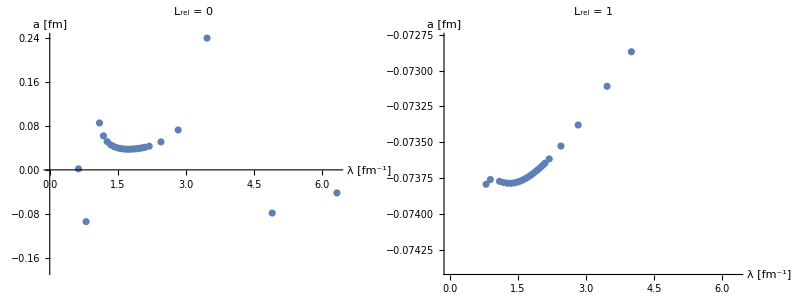

```mathematica
Λl=√(4 Transpose[LCD]⟦1⟧);
αl=Transpose[LCD]⟦2⟧;
C0l=Transpose[LCD]⟦3⟧;
D0l=Transpose[LCD]⟦4⟧;

LEC0s={};
LED0s={};
αs={};
λs={};
a0s={};
affs={};

cotDsofPandL={};
atfstarsp={};
rtfstarsp={};
atfstarss={};
rtfstarss={};

(*Λl={1};*)


Do[{

Λ=Λl⟦j⟧;
λ=Transpose[LCD]⟦1⟧⟦j⟧;
α=αl⟦j⟧;
C0=C0l⟦j⟧;
D0=D0l⟦j⟧;



AppendTo[LEC0s,     C0];
AppendTo[αs,     α];
AppendTo[λs,    λ];

L=0;

(*Print parameters of the calculation*)
Print[Style[{"λ = ", λ,"   C0 = ", C0,"   D0 = ",D0},Blue,Bold,8]];



(* Microscopic calculation: *)
μ1=m/2;hbar=197.327053;mh2=(2 μ1)/(hbar)^2;
V0[r_]                   := C0  Exp[- λ r^2];
Vα0[Cc_,r_]       :=Cc  ⅇ^(-λ r^2);
W[r_,rp_,e_]  :=0;



(*Fit of the two body *)
If[Fit2b,
R=5;
C0=x/.FindRoot[Scatt1[x]^-1==aleph,{x,0.}];
Print["Fit try: C0: ",C0,"  a=",Scatt1[C0]];];



(*Calculate fermion fermion*)
If[CalculateFF,
Print[Style[{" * Fermion - Fermion scattering * "},Blue,Italic,8]];

nGrid     =100;
R             =10;
aff=SolveSecularNL0[R,nGrid,0.0]⟦1⟧;
(*Print[aamat//MatrixForm];*)

R=5;
Print[" > Finite Difference Method: a_ff = ", aff ];
Print[" > Variational Phase Method: aff = ",Scatt1[C0]];
aleph=aff^-1; (*Scatt1[C0]^-1;*)
α=1.5 5  aleph^2; (* useless if then you fit the correct dimer-dimer a*)
AppendTo[affs,    aff];
Print[""]];













If[Calculate4H,
(** Trimer - Fermion case^4 H **)
Print[Style[{" * Fermion - Trimer star scattering * "},Blue,Italic,8]];

hbar=1;E3=-8.48;
R3=(-2m E3/hbar^2)^(-1/2);
α=R3;
Print["α3 is ", α];

Lrel=1;

(* Trimer - Fermion case^4 H *)
μ1=3/4 m;hbar=197.327053;mh2=(2 μ1)/(hbar)^2;
(* L = 1 --------------------------------------------------------------------------------------- *)
η2=2 C0((3α)/(3α+λ))^(3/2);η3=8D0((3 α^2)/(12 α^2+16α λ+λ^2))^(3/2);
ω2=(3 α λ)/(3α+λ);ω3=(12α λ(α+λ))/(12 α^2+16α λ+λ^2);
ξ1=27/8(3/2 α)^(3/2)mh2^-1;ξ2=-2 27 (3/2 α)^(3/2)C0(α/(4α+λ))^(3/2);ξ3=-27(3/2 α)^(3/2)D0(α/(4α+5 λ))^(3/2);

a1=15/16 α;a2=(3α(5α+8λ))/(4(4α+λ));a3=(3(20 α^2+52α λ+27 λ^2))/(4(16α+20λ));
b1=18/16 α;b2=(9α(α+λ))/(2(4α+λ));b3=(9(4 α^2+8α λ+3 λ^2))/(2(16α+20λ));
c1=15/16 α;c2=(3α(5α+2λ))/(4(4α+λ));c3=(3(20 α^2+28α λ+3 λ^2))/(4(16α+20λ));


V0[r_]:=η2 ⅇ^(-ω2  r^2)+η3 ⅇ^(-ω3  r^2);
WP[r_,rp_,p_]:=Re[-(r rp 4 π)(ξ1  ⅇ^(-a1 r^2- c1 rp^2) ((-(4 a1^2 r^2+b1^2 rp^2-2 a1)+2/r^2-p^2) ⅈ SphericalBesselJ[1,ⅈ b1 r rp]-4 a1 b1 r rp (SphericalBesselJ[0,ⅈ b1 r rp]/Sqrt[3]
-SphericalBesselJ[2,ⅈ b1 r rp] 2/Sqrt[15]))+ξ2 ⅈ SphericalBesselJ[1,ⅈ b2 r rp] ⅇ^(-a2 r^2- c2 rp^2)+ ξ3 ⅈ SphericalBesselJ[1,ⅈ b3 r rp] ⅇ^(-a3 r^2- c3 rp^2))];


(* Fermion - Trimer finite momentum *)
nGrid=200;
Rmax=7;
Pp={0.001,0.002,0.003,0.004,0.005,0.007,0.008,0.009,0.01,0.02};
Pp={0.001,0.005,0.01, 0.05, 0.1};
Tp={};
(*Print["       **  p         T            a"];*)

SetSharedVariable[TppP];
TppP=Pp;

ParallelDo[
Ti=ArcTan[SolveSecularNL1[Rmax,nGrid,Pp⟦i⟧,Lrel]⟦1⟧];

(*Print["       **  ",Pp⟦i⟧,"   " ,-Ti/Pp⟦i⟧^(2 Lrel+1)];*)
TppP⟦i⟧=-Ti/Pp⟦i⟧^(2 Lrel+1);
,{i,Range[Length[Pp]]}
];


dataP=Transpose[{Pp,TppP}];
Ere=Fit[dataP,{1,p^2},p];
a1tfP=-Coefficient[Ere,p,0]^-1;
r1tfP= Coefficient[Ere,p,2]*2.;

AppendTo[atfstarsp,    a1tfP];
AppendTo[rtfstarsp,    r1tfP];

(* L = 0 --------------------------------------------------------------------------------------- *)

WS[r_,rp_,p_]:=Re[-(r rp 4 π)(ξ1  ⅇ^(-a1 r^2- c1 rp^2) ((-(4 a1^2 r^2+b1^2 rp^2-2 a1)-p^2) ⅈ SphericalBesselJ[0,ⅈ b1 r rp]-4 a1 b1 r rp SphericalBesselJ[1,ⅈ b1 r rp] ⅈ/Sqrt[3]
)+ξ2 SphericalBesselJ[0,ⅈ b2 r rp] ⅇ^(-a2 r^2- c2 rp^2)+ ξ3 SphericalBesselJ[0,ⅈ b3 r rp] ⅇ^(-a3 r^2- c3 rp^2))];
SetSharedVariable[TppS];
TppS=Pp;

ParallelDo[
Ti=ArcTan[SolveSecularNL0[Rmax,nGrid,Pp⟦i⟧]⟦1⟧];

(*Print["       **  ",Pp⟦i⟧,"   " ,-Ti/Pp⟦i⟧^(2 Lrel+1)];*)
TppS⟦i⟧=-Ti/Pp⟦i⟧;
,{i,Range[Length[Pp]]}
];


dataS=Transpose[{Pp,TppS}];
Ere=Fit[dataS,{1,p^2},p];
a1tfS=-Coefficient[Ere,p,0]^-1;
r1tfS= Coefficient[Ere,p,2]*2.;

AppendTo[cotDsofPandL,dataS];

AppendTo[atfstarss,    a1tfS];
AppendTo[rtfstarss,    r1tfS];

Print["L = 0: (finite momentum)   a_(t - f) = ",a1tfS, "     r_(t - f) = ", r1tfS];
Print["L = 1: (finite momentum)   a_(t - f) = ",a1tfP, "     r_(t - f) = ", r1tfP];

(*ListPlot[data,GridLines->{{},{-2π,-1.5π,-π,-0.5π,0,0.5π,1π,1.5π,2π}}]//Print;*)
(*Show[ListPlot[data,GridLines->{{},{-2π,-1.5π,-π,-0.5π,0,0.5π,1π,1.5π,2π}}],Plot[Ere,{p,0,Pp⟦-1⟧}]]//Print;
Print[">> The pole is at: ", Solve[-a1tf^-1+0.5 r1tf p^2-ⅈ p^3 ==0,p]];
*)
];




Print[" -- "];
Print[" "];
Print[" "];
},{j,1,Length[Λl]}];

Grid[{{ListPlot[Transpose[{Λl,atfstarss}],AxesLabel->{"λ [fm^-1]","a [fm]"},PlotLabel->"L_rel = 0",ImageSize->400],ListPlot[Transpose[{Λl,atfstarsp}],AxesLabel->{"λ [fm^-1]","a [fm]"},PlotLabel->"L_rel = 1",ImageSize->400]}}]
```

```mathematica
Do[{ sol=Solve[-atfstarsp⟦i⟧^-1+0.5 rtfstarsp⟦i⟧ p^2-ⅈ p^3 ==0,p];
Print["Λ = ",Λl⟦i⟧,"    Re(p) = ",Abs[Re[p/.sol⟦1⟧]],"   Im(p) = ",Im[p/.sol⟦1⟧]];
Print["E = ", Re[mh2^-1(p/.sol⟦1⟧)^2], "     Γ = ",Im[ mh2^-1(p/.sol⟦1⟧)^2]*2];
},{i,1,Length[rtfstarsp]}];
```

Λ = 0.632456    Re(p) = 0.26115   Im(p) = -0.000174903

E = 1.88553     Γ = 0.00505129

Λ = 0.8    Re(p) = 0.26268   Im(p) = -0.000175666

E = 1.90769     Γ = 0.00510304

Λ = 0.894427    Re(p) = 0.262658   Im(p) = -0.000175528

E = 1.90737     Γ = 0.0050986

Λ = 1.09545    Re(p) = 0.262591   Im(p) = -0.000175377

E = 1.90639     Γ = 0.00509291

Λ = 1.18322    Re(p) = 0.26257   Im(p) = -0.000175342

E = 1.90609     Γ = 0.00509148

Λ = 1.26491    Re(p) = 0.262557   Im(p) = -0.000175318

E = 1.9059     Γ = 0.00509055

Λ = 1.34164    Re(p) = 0.26255   Im(p) = -0.000175302

E = 1.9058     Γ = 0.00508994

Λ = 1.41421    Re(p) = 0.262548   Im(p) = -0.000175291

E = 1.90577     Γ = 0.00508956

Λ = 1.48324    Re(p) = 0.262549   Im(p) = -0.000175282

E = 1.90579     Γ = 0.00508935

Λ = 1.54919    Re(p) = 0.262553   Im(p) = -0.000175276

E = 1.90585     Γ = 0.00508925

Λ = 1.61245    Re(p) = 0.26256   Im(p) = -0.000175272

E = 1.90594     Γ = 0.00508925

Λ = 1.67332    Re(p) = 0.262568   Im(p) = -0.000175269

E = 1.90606     Γ = 0.00508932

Λ = 1.73205    Re(p) = 0.262577   Im(p) = -0.000175267

E = 1.90619     Γ = 0.00508945

Λ = 1.78885    Re(p) = 0.262587   Im(p) = -0.000175266

E = 1.90634     Γ = 0.00508961

Λ = 1.84391    Re(p) = 0.262599   Im(p) = -0.000175265

E = 1.90651     Γ = 0.00508981

Λ = 1.89737    Re(p) = 0.26261   Im(p) = -0.000175265

E = 1.90668     Γ = 0.00509004

Λ = 1.94936    Re(p) = 0.262623   Im(p) = -0.000175266

E = 1.90686     Γ = 0.00509029

Λ = 2    Re(p) = 0.262636   Im(p) = -0.000175266

E = 1.90704     Γ = 0.00509056

Λ = 2.04939    Re(p) = 0.262649   Im(p) = -0.000175267

E = 1.90723     Γ = 0.00509084

Λ = 2.09762    Re(p) = 0.262662   Im(p) = -0.000175268

E = 1.90743     Γ = 0.00509113

Λ = 2.19089    Re(p) = 0.26269   Im(p) = -0.000175271

E = 1.90783     Γ = 0.00509174

Λ = 2.44949    Re(p) = 0.262774   Im(p) = -0.000175282

E = 1.90905     Γ = 0.00509369

Λ = 2 √2    Re(p) = 0.262913   Im(p) = -0.000175303

E = 1.91107     Γ = 0.005097

Λ = 2 √3    Re(p) = 0.263171   Im(p) = -0.000175345

E = 1.91482     Γ = 0.00510323

Λ = 4    Re(p) = 0.263402   Im(p) = -0.000175383

E = 1.91818     Γ = 0.00510882

Λ = 2 √6    Re(p) = 0.263802   Im(p) = -0.000175447

E = 1.92402     Γ = 0.00511843

Λ = 2 √10    Re(p) = 0.264445   Im(p) = -0.000175536

E = 1.93341     Γ = 0.00513351